```mathematica
Σph11[t_,U_,ω_]:=U/2+(U^2 t)/(4 √(4 t^2-2 t U))(1/(ω-(t+√(4 t^2-2 t U)))+1/(ω+(t+√(4 t^2-2 t U))))
Σph12[t_,U_,ω_]:=(U^2 t)/(4 √(4 t^2-2 t U))(1/(ω-(t+√(4 t^2-2 t U)))-1/(ω+(t+√(4 t^2-2 t U))))
Oph11[t_,U_,ω_]:=U-(U^2 t)/(2 √(4 t^2-2 t U))(1/(ω-(√(4 t^2-2 t U)))-1/(ω+(√(4 t^2-2 t U))))
Oph12[t_,U_,ω_]:=(U^2 t)/(2 √(4 t^2-2 t U))(1/(ω-(√(4 t^2-2 t U)))-1/(ω+(√(4 t^2-2 t U))))
Σphvv[t_,U_,ω_]:=Σph11[t,U,ω]+Σph12[t,U,ω] 
Σphcc[t_,U_,ω_]:=Σph11[t,U,ω]-Σph12[t,U,ω]  
dΣphvv[t_,U_,ω_]:=-((t U^2)/(4 √(4 t^2-2 t U)))((1/((-t-√(4 t^2-2t U)+ω)^2)-1/((t+√(4 t^2-2 t U)+ω)^2))+ (1/((-t-√(4 t^2-2 t U)+ω)^2)+1/((t+√(4 t^2-2 t U)+ω)^2)))
dΣphcc[t_,U_,ω_]:=-((t U^2)/(4 √(4 t^2-2 t U)))(- (1/((-t-√(4 t^2-2 t U)+ω)^2)-1/((t+√(4 t^2-2 t U)+ω)^2))+ (1/((-t-√(4 t^2-2 t U)+ω)^2)+1/((t+√(4 t^2-2 t U)+ω)^2)))

ϵphv[t_,U_]:=-t+1/(1-dΣphvv[t,U,-t])Σphvv[t,U,-t]
ϵphc[t_,U_]:=t+1/(1-dΣphcc[t,U,t])Σphcc[t,U,t]
Δϵppl[t_,U_]:=(2 (-16 t^2-5 t U+8 √2 t √(t (2 t+U))+√2 U √(t (2 t+U))))/U
Δϵphl[t_,U_]:=(2 (16 t^2-8 √2 t √(t (2 t-U))-5 t U+√2 √(t (2 t-U)) U))/U
ΔϵgwL[t_,U_]:=(64 t^3+96 t^2 U+26 t U^2-32 t U √(t (t+U))-4 U^2 √(t (t+U)))/(32 t^2+32 t U-U^2)
```

```mathematica
ℰ23as[t_,U_,Δv_]:=2/3 (U+ √(12 t^2+U^2+3 Δv^2) Cos[1/3 ArcCos[-(U (18 t^2+U^2-9 Δv^2))/((12 t^2+U^2+3 Δv^2)^(3/2))]])
ℰ22as[t_,U_,Δv_]:=2/3 (U- √(12 t^2+U^2+3 Δv^2) Cos[1/3 (π+ArcCos[-(U (18 t^2+U^2-9 Δv^2))/((12 t^2+U^2+3 Δv^2)^(3/2))])])
ℰ21as=0;
ℰ20as[t_,U_,Δv_]:=2/3 (U- √(12 t^2+U^2+3 Δv^2) Sin[1/6 (π+2 ArcCos[-(U (18 t^2+U^2-9 Δv^2))/((12 t^2+U^2+3 Δv^2)^(3/2))])])
ωEAexcas[t_,U_,Δv_]:=1/6 (2 U-3 t √(4+Δv^2/t^2)+4 t √((12 t^2+U^2+3 Δv^2)/t^2) Sin[1/6 (π+2 ArcCos[-(U (18 t^2+U^2-9 Δv^2))/(t^3 ((12 t^2+U^2+3 Δv^2)/t^2)^(3/2))])])
ωEIexcas[t_,U_,Δv_]:=1/6 (4 U+3 t √(4+Δv^2/t^2)-4 t √((12 t^2+U^2+3 Δv^2)/t^2) Sin[1/6 (π+2 ArcCos[-(U (18 t^2+U^2-9 Δv^2))/(t^3 ((12 t^2+U^2+3 Δv^2)/t^2)^(3/2))])])
excas1[t_,U_,Δv_]:= - ℰ20as[t,U,Δv]
excas2[t_,U_,Δv_]:= ℰ22as[t,U,Δv]- ℰ20as[t,U,Δv]
Egap[t_,U_,Δv_]     :=ωEAexcas[t,U,Δv]-ωEIexcas[t,U,Δv]
Eb1exc[t_,U_,Δv_]:=Egap[t,U,Δv]-excas1[t,U,Δv]
Eb2exc[t_,U_,Δv_]:=Egap[t,U,Δv]-excas2[t,U,Δv]
```

```mathematica
(*Avec G^HF*)
```

```mathematica
Ω[t_,U_]:=√(4 t^2-2t U)
```

```mathematica
Σ11[t_,U_,ω_]:=(U^2 t)/(4 √(4 t^2-2 t U))(1/(ω-(t+√(4 t^2-2 t U)+U/2))+1/(ω+(t+√(4 t^2-2 t U)-U/2)))
Σ12[t_,U_,ω_]:=(U^2 t)/(4 √(4 t^2-2 t U))(1/(ω-(t+√(4 t^2-2 t U)+U/2))-1/(ω+(t+√(4 t^2-2 t U)-U/2)))

Σvv[t_,U_,ω_]:=Σ11[t,U,ω]+Σ12[t,U,ω] 
Σcc[t_,U_,ω_]:=Σ11[t,U,ω]-Σ12[t,U,ω]  
dΣvv[t_,U_,ω_]:=-(U^2 t)/(2 √(4 t^2-2 t U))1/((ω-(t+√(4 t^2-2 t U)+U/2))^2)
dΣcc[t_,U_,ω_]:=-(U^2 t)/(2 √(4 t^2-2 t U))1/((ω+(t+√(4 t^2-2 t U)-U/2))^2)

ϵv[t_,U_]:=-t+U/2+1/(1-dΣvv[t,U,-t+U/2])Σvv[t,U,-t+U/2]
ϵc[t_,U_]:=t+U/2+1/(1-dΣcc[t,U,t+U/2])Σcc[t,U,t+U/2]
```

```mathematica
vt1phl[t_,U_]:=-1/(2 U (-2 t+U))(√(32768 t^6+4 t U^4 (-16 √2 √(t (2 t-U))+U)+U^5 (-8 √2 √(t (2 t-U))+U)-2048 t^5 (8 √2 √(t (2 t-U))+27 U)+16 t^2 U^3 (134 √2 √(t (2 t-U))+51 U)-32 t^3 U^2 (364 √2 √(t (2 t-U))+281 U)+64 t^4 U (368 √2 √(t (2 t-U))+533 U)))
```

```mathematica
vs1phl[t_,U_]:=-1/(2 U (-2 t+U))(√(32768 t^6+U^5 (8 √2 √(t (2 t-U))+U)-608 t^3 U^2 (20 √2 √(t (2 t-U))+17 U)-4 t U^4 (64 √2 √(t (2 t-U))+19 U)-2048 t^5 (8 √2 √(t (2 t-U))+27 U)+16 t^2 U^3 (170 √2 √(t (2 t-U))+87 U)+64 t^4 U (368 √2 √(t (2 t-U))+549 U)))
```

```mathematica
Series[vt1phl[t,U],{U,0,4},Assumptions->t>0]//FullSimplify
```

2 t-U/2+U^2/(16 t)-U^3/(32 t^2)-(47 U^4)/(1024 t^3)+O[U]^(9/2)

```mathematica
QPgw1[t_,U_]:=1/4 (-8 √(t (t+U))+2 √((2 t U^2)/(√(t (t+U)))+1/4 (4 t+U+4 √(t (t+U)))^2)+√((32 t^3+U^3+8 t^2 (5 U+4 √(t (t+U)))+3 t U (3 U+8 √(t (t+U))))/(t+U)))
Δϵgwstat[t_,U_]:=2*t+(2 U^2*t(t+Sqrt[4 t^2+4*t*U]))/((4 t^2+4*t*U)*(2t+Sqrt[4 t^2+4*t*U]))
ΔϵgwL[t_,U_]:=(64 t^3+96 t^2 U+26 t U^2-32 t U √(t (t+U))-4 U^2 √(t (t+U)))/(32 t^2+32 t U-U^2)
Δϵstateh[t_,U_]:=2*t+(U^2*t)/(Sqrt[4 t^2-2*t*U]*(t+Sqrt[4 t^2-2*t*U]))
Δϵdyneh[t_,U_]:=1/4 (-4 √2 √(t (2 t-U))+2 √((t U^2)/(√(t^2-(t U)/2))+(2 t-U/2+√(4 t^2-2 t U))^2)+2 √((t U^2)/(√(t^2-(t U)/2))+(2 t+U/2+√(4 t^2-2 t U))^2))
ΔeQP[t_,U_]:=-2t+Sqrt[16 t^2+U^2]
```

```mathematica
Htgw[Δϵ_,t_,U_]:=({{Δϵ-U/2, U^2/(2(t+U))-U/2}, {-(U^2/(2(t+U))-U/2), -(Δϵ-U/2)}})
Hsgw[Δϵ_,t_,U_]:=({{Δϵ+U/2, U^2/(2(t+U))+U/2}, {-(U^2/(2(t+U))+U/2), -(Δϵ+U/2)}})
Htph[Δϵ_,t_,U_]:=({{Δϵ-U/2, -(U t)/(2t-U)}, {(U t)/(2t-U), -(Δϵ-U/2)}})
Hsph[Δϵ_,t_,U_]:=({{Δϵ+U/2, (U t)/(2t-U)}, {-(U t)/(2t-U), -(Δϵ+U/2)}})
```

```mathematica
vtgwgz[t_,U_]:=(√(16 t^4+24 t^3 U-6 t U^3+U^4))/(2 (t+U))
vsgwgz[t_,U_]:=(√((4 t^2+4 t U-U^2) (4 t^2+6 t U+3 U^2)))/(2 (t+U))
vtgwstat[t_,U_]:=(t √(128 t^4+U^3 (U-12 √(t (t+U)))+128 t^3 (2 U+√(t (t+U)))+48 t^2 U (3 U+4 √(t (t+U)))+4 t U^2 (5 U+12 √(t (t+U)))))/(4 (t+U) (t+√(t (t+U))))
vsgwstat[t_,U_]:=(√(t (128 t^5-8 U^4 √(t (t+U))+128 t^4 (3 U+√(t (t+U)))+16 t^3 U (29 U+20 √(t (t+U)))+3 t U^3 (19 U+36 √(t (t+U)))+4 t^2 U^2 (67 U+76 √(t (t+U))))))/(4 (t+U) (t+√(t (t+U))))
vtgwlin[t_,U_]:=1/(2 (t+U) (32 t^2+32 t U-U^2))(√(16384 t^8+73728 t^7 U+16 t^4 U^3 (3701 U-4160 √(t (t+U)))+16 t^2 U^5 (126 U-377 √(t (t+U)))+2 t U^6 (53 U-240 √(t (t+U)))+U^7 (U-16 √(t (t+U)))-1024 t^6 U (-129 U+16 √(t (t+U)))-512 t^5 U^2 (-235 U+108 √(t (t+U)))-8 t^3 U^4 (-1945 U+4152 √(t (t+U)))))
vsgwlin[t_,U_]:=1/(2 (t+U) (32 t^2+32 t U-U^2))(√(16384 t^8+90112 t^7 U+16 t^2 U^5 (244 U-1047 √(t (t+U)))-1024 t^6 U (-201 U+16 √(t (t+U)))+U^7 (-3 U+16 √(t (t+U)))-512 t^5 U^2 (-479 U+124 √(t (t+U)))-2 t U^6 (-75 U+592 √(t (t+U)))-16 t^4 U^3 (-9701 U+5760 √(t (t+U)))-8 t^3 U^4 (-5727 U+7576 √(t (t+U)))))
```

```mathematica
vtgwdyn[t_,U_]:=1/(2 √2 (t+U))(√(64 t^4+176 t^3 U+161 t^2 U^2+54 t U^3+3 U^4+32 t^3 √(t (t+U))+80 t^2 U √(t (t+U))+72 t U^2 √(t (t+U))+24 U^3 √(t (t+U))-4 t^2 U √((2 t U^2)/(√(t (t+U)))+1/4 (4 t+U+4 √(t (t+U)))^2)-8 t U^2 √((2 t U^2)/(√(t (t+U)))+1/4 (4 t+U+4 √(t (t+U)))^2)-4 U^3 √((2 t U^2)/(√(t (t+U)))+1/4 (4 t+U+4 √(t (t+U)))^2)-16 t^2 √(t (t+U)) √((2 t U^2)/(√(t (t+U)))+1/4 (4 t+U+4 √(t (t+U)))^2)-32 t U √(t (t+U)) √((2 t U^2)/(√(t (t+U)))+1/4 (4 t+U+4 √(t (t+U)))^2)-16 U^2 √(t (t+U)) √((2 t U^2)/(√(t (t+U)))+1/4 (4 t+U+4 √(t (t+U)))^2)-2 t^2 U √((32 t^3+U^3+8 t^2 (5 U+4 √(t (t+U)))+3 t U (3 U+8 √(t (t+U))))/(t+U))-4 t U^2 √((32 t^3+U^3+8 t^2 (5 U+4 √(t (t+U)))+3 t U (3 U+8 √(t (t+U))))/(t+U))-2 U^3 √((32 t^3+U^3+8 t^2 (5 U+4 √(t (t+U)))+3 t U (3 U+8 √(t (t+U))))/(t+U))-8 t^2 √(t (t+U)) √((32 t^3+U^3+8 t^2 (5 U+4 √(t (t+U)))+3 t U (3 U+8 √(t (t+U))))/(t+U))-16 t U √(t (t+U)) √((32 t^3+U^3+8 t^2 (5 U+4 √(t (t+U)))+3 t U (3 U+8 √(t (t+U))))/(t+U))-8 U^2 √(t (t+U)) √((32 t^3+U^3+8 t^2 (5 U+4 √(t (t+U)))+3 t U (3 U+8 √(t (t+U))))/(t+U))+2 t^2 √((2 t U^2)/(√(t (t+U)))+1/4 (4 t+U+4 √(t (t+U)))^2) √((32 t^3+U^3+8 t^2 (5 U+4 √(t (t+U)))+3 t U (3 U+8 √(t (t+U))))/(t+U))+4 t U √((2 t U^2)/(√(t (t+U)))+1/4 (4 t+U+4 √(t (t+U)))^2) √((32 t^3+U^3+8 t^2 (5 U+4 √(t (t+U)))+3 t U (3 U+8 √(t (t+U))))/(t+U))+2 U^2 √((2 t U^2)/(√(t (t+U)))+1/4 (4 t+U+4 √(t (t+U)))^2) √((32 t^3+U^3+8 t^2 (5 U+4 √(t (t+U)))+3 t U (3 U+8 √(t (t+U))))/(t+U))))
```

```mathematica
vsgwdyn[t_,U_]:=1/(2 √2 (t+U))(√(64 t^4+176 t^3 U+161 t^2 U^2+46 t U^3-5 U^4+32 t^3 √(t (t+U))+48 t^2 U √(t (t+U))+8 t U^2 √(t (t+U))-8 U^3 √(t (t+U))+4 t^2 U √((2 t U^2)/(√(t (t+U)))+1/4 (4 t+U+4 √(t (t+U)))^2)+8 t U^2 √((2 t U^2)/(√(t (t+U)))+1/4 (4 t+U+4 √(t (t+U)))^2)+4 U^3 √((2 t U^2)/(√(t (t+U)))+1/4 (4 t+U+4 √(t (t+U)))^2)-16 t^2 √(t (t+U)) √((2 t U^2)/(√(t (t+U)))+1/4 (4 t+U+4 √(t (t+U)))^2)-32 t U √(t (t+U)) √((2 t U^2)/(√(t (t+U)))+1/4 (4 t+U+4 √(t (t+U)))^2)-16 U^2 √(t (t+U)) √((2 t U^2)/(√(t (t+U)))+1/4 (4 t+U+4 √(t (t+U)))^2)+2 t^2 U √((32 t^3+U^3+8 t^2 (5 U+4 √(t (t+U)))+3 t U (3 U+8 √(t (t+U))))/(t+U))+4 t U^2 √((32 t^3+U^3+8 t^2 (5 U+4 √(t (t+U)))+3 t U (3 U+8 √(t (t+U))))/(t+U))+2 U^3 √((32 t^3+U^3+8 t^2 (5 U+4 √(t (t+U)))+3 t U (3 U+8 √(t (t+U))))/(t+U))-8 t^2 √(t (t+U)) √((32 t^3+U^3+8 t^2 (5 U+4 √(t (t+U)))+3 t U (3 U+8 √(t (t+U))))/(t+U))-16 t U √(t (t+U)) √((32 t^3+U^3+8 t^2 (5 U+4 √(t (t+U)))+3 t U (3 U+8 √(t (t+U))))/(t+U))-8 U^2 √(t (t+U)) √((32 t^3+U^3+8 t^2 (5 U+4 √(t (t+U)))+3 t U (3 U+8 √(t (t+U))))/(t+U))+2 t^2 √((2 t U^2)/(√(t (t+U)))+1/4 (4 t+U+4 √(t (t+U)))^2) √((32 t^3+U^3+8 t^2 (5 U+4 √(t (t+U)))+3 t U (3 U+8 √(t (t+U))))/(t+U))+4 t U √((2 t U^2)/(√(t (t+U)))+1/4 (4 t+U+4 √(t (t+U)))^2) √((32 t^3+U^3+8 t^2 (5 U+4 √(t (t+U)))+3 t U (3 U+8 √(t (t+U))))/(t+U))+2 U^2 √((2 t U^2)/(√(t (t+U)))+1/4 (4 t+U+4 √(t (t+U)))^2) √((32 t^3+U^3+8 t^2 (5 U+4 √(t (t+U)))+3 t U (3 U+8 √(t (t+U))))/(t+U))))
```

```mathematica
vtgwΔϵQP[t_,U_]:=1/(2 (t+U))(√(80 t^4+4 t^2 U (25 U-9 √(16 t^2+U^2))+6 t U^2 (3 U-4 √(16 t^2+U^2))+U^3 (5 U-4 √(16 t^2+U^2))+8 t^3 (21 U-2 √(16 t^2+U^2))))
vsgwΔϵQP[t_,U_]:=1/(2 (t+U))(√(80 t^4+4 t^2 U (17 U-7 √(16 t^2+U^2))+8 t^3 (19 U-2 √(16 t^2+U^2))-2 t U^2 (U+4 √(16 t^2+U^2))+U^3 (U+4 √(16 t^2+U^2))))
```

```mathematica
vtphgz[t_,U_]:=(√((8 t^2-8 t U+U^2) (8 t^2-4 t U+U^2)))/(4 t-2 U)
vsphgz[t_,U_]:=(√((8 t^2-U^2) (8 t^2-4 t U-U^2)))/(4 t-2 U)
```

```mathematica
vtphstat[t_,U_]:=1/(2 (t+√2 √(t (2 t-U))) (t (2 t-U))^(3/2))t √(t^2 (2 t-U) (320 t^5+32 t^4 (4 √2 √(t (2 t-U))-19 U)+4 t^2 (28 √2 √(t (2 t-U))-59 U) U^2+4 (√2 √(t (2 t-U))-2 U) U^4+16 t^3 U (-12 √2 √(t (2 t-U))+31 U)+t U^3 (-36 √2 √(t (2 t-U))+65 U)))
vsphstat[t_,U_]:=(t √(t^3 (2 t-U) (320 t^4+32 t^3 (4 √2 √(t (2 t-U))-9 U)+4 t U^2 (-4 √2 √(t (2 t-U))+U)+U^3 (4 √2 √(t (2 t-U))+U)+16 t^2 U (-4 √2 √(t (2 t-U))+3 U))))/(2 (t+√2 √(t (2 t-U))) (t (2 t-U))^(3/2))
```

```mathematica
vtphdyn[t_,U_]:=1/(4 t-2 U)(√(128 t^4+32 √2 t^3 √(t (2 t-U))-176 t^3 U-16 √2 t^2 √(t (2 t-U)) U+82 t^2 U^2-4 √2 t √(t (2 t-U)) U^2-18 t U^3+2 √2 √(t (2 t-U)) U^3+(3 U^4)/2-16 √2 t^2 √(t (2 t-U)) √((t U^2)/(√(t^2-(t U)/2))+(2 t-U/2+√(4 t^2-2 t U))^2)-8 t^2 U √((t U^2)/(√(t^2-(t U)/2))+(2 t-U/2+√(4 t^2-2 t U))^2)+16 √2 t √(t (2 t-U)) U √((t U^2)/(√(t^2-(t U)/2))+(2 t-U/2+√(4 t^2-2 t U))^2)+8 t U^2 √((t U^2)/(√(t^2-(t U)/2))+(2 t-U/2+√(4 t^2-2 t U))^2)-4 √2 √(t (2 t-U)) U^2 √((t U^2)/(√(t^2-(t U)/2))+(2 t-U/2+√(4 t^2-2 t U))^2)-2 U^3 √((t U^2)/(√(t^2-(t U)/2))+(2 t-U/2+√(4 t^2-2 t U))^2)-16 √2 t^2 √(t (2 t-U)) √((t U^2)/(√(t^2-(t U)/2))+(2 t+U/2+√(4 t^2-2 t U))^2)-8 t^2 U √((t U^2)/(√(t^2-(t U)/2))+(2 t+U/2+√(4 t^2-2 t U))^2)+16 √2 t √(t (2 t-U)) U √((t U^2)/(√(t^2-(t U)/2))+(2 t+U/2+√(4 t^2-2 t U))^2)+8 t U^2 √((t U^2)/(√(t^2-(t U)/2))+(2 t+U/2+√(4 t^2-2 t U))^2)-4 √2 √(t (2 t-U)) U^2 √((t U^2)/(√(t^2-(t U)/2))+(2 t+U/2+√(4 t^2-2 t U))^2)-2 U^3 √((t U^2)/(√(t^2-(t U)/2))+(2 t+U/2+√(4 t^2-2 t U))^2)+8 t^2 √((t U^2)/(√(t^2-(t U)/2))+(2 t-U/2+√(4 t^2-2 t U))^2) √((t U^2)/(√(t^2-(t U)/2))+(2 t+U/2+√(4 t^2-2 t U))^2)-8 t U √((t U^2)/(√(t^2-(t U)/2))+(2 t-U/2+√(4 t^2-2 t U))^2) √((t U^2)/(√(t^2-(t U)/2))+(2 t+U/2+√(4 t^2-2 t U))^2)+2 U^2 √((t U^2)/(√(t^2-(t U)/2))+(2 t-U/2+√(4 t^2-2 t U))^2) √((t U^2)/(√(t^2-(t U)/2))+(2 t+U/2+√(4 t^2-2 t U))^2)))
```

```mathematica
vsphdyn[t_,U_]:=1/(4 t-2 U)(√(128 t^4+32 √2 t^3 √(t (2 t-U))-176 t^3 U-48 √2 t^2 √(t (2 t-U)) U+82 t^2 U^2+28 √2 t √(t (2 t-U)) U^2-18 t U^3-6 √2 √(t (2 t-U)) U^3+(3 U^4)/2-16 √2 t^2 √(t (2 t-U)) √((t U^2)/(√(t^2-(t U)/2))+(2 t-U/2+√(4 t^2-2 t U))^2)+8 t^2 U √((t U^2)/(√(t^2-(t U)/2))+(2 t-U/2+√(4 t^2-2 t U))^2)+16 √2 t √(t (2 t-U)) U √((t U^2)/(√(t^2-(t U)/2))+(2 t-U/2+√(4 t^2-2 t U))^2)-8 t U^2 √((t U^2)/(√(t^2-(t U)/2))+(2 t-U/2+√(4 t^2-2 t U))^2)-4 √2 √(t (2 t-U)) U^2 √((t U^2)/(√(t^2-(t U)/2))+(2 t-U/2+√(4 t^2-2 t U))^2)+2 U^3 √((t U^2)/(√(t^2-(t U)/2))+(2 t-U/2+√(4 t^2-2 t U))^2)-16 √2 t^2 √(t (2 t-U)) √((t U^2)/(√(t^2-(t U)/2))+(2 t+U/2+√(4 t^2-2 t U))^2)+8 t^2 U √((t U^2)/(√(t^2-(t U)/2))+(2 t+U/2+√(4 t^2-2 t U))^2)+16 √2 t √(t (2 t-U)) U √((t U^2)/(√(t^2-(t U)/2))+(2 t+U/2+√(4 t^2-2 t U))^2)-8 t U^2 √((t U^2)/(√(t^2-(t U)/2))+(2 t+U/2+√(4 t^2-2 t U))^2)-4 √2 √(t (2 t-U)) U^2 √((t U^2)/(√(t^2-(t U)/2))+(2 t+U/2+√(4 t^2-2 t U))^2)+2 U^3 √((t U^2)/(√(t^2-(t U)/2))+(2 t+U/2+√(4 t^2-2 t U))^2)+8 t^2 √((t U^2)/(√(t^2-(t U)/2))+(2 t-U/2+√(4 t^2-2 t U))^2) √((t U^2)/(√(t^2-(t U)/2))+(2 t+U/2+√(4 t^2-2 t U))^2)-8 t U √((t U^2)/(√(t^2-(t U)/2))+(2 t-U/2+√(4 t^2-2 t U))^2) √((t U^2)/(√(t^2-(t U)/2))+(2 t+U/2+√(4 t^2-2 t U))^2)+2 U^2 √((t U^2)/(√(t^2-(t U)/2))+(2 t-U/2+√(4 t^2-2 t U))^2) √((t U^2)/(√(t^2-(t U)/2))+(2 t+U/2+√(4 t^2-2 t U))^2)))
```

```mathematica
vtQPph[t_,U_]:=(√(320 t^4-12 t U^3+U^3 (5 U-4 √(16 t^2+U^2))-32 t^3 (9 U+2 √(16 t^2+U^2))+16 t^2 U (4 U+3 √(16 t^2+U^2))))/(4 t-2 U)
vsQPph[t_,U_]:=1/(4 t-2 U)(√(320 t^4-32 t^3 (11 U+2 √(16 t^2+U^2))+U^3 (5 U+4 √(16 t^2+U^2))+16 t^2 U (8 U+5 √(16 t^2+U^2))-4 t U^2 (7 U+8 √(16 t^2+U^2))))
```

```mathematica
vtstatΣgwTpptriplet[t_,U_]:=1/(4 (t+U) (2 t+U) (t+√(t (t+U))))t √(512 t^6+1536 t^5 U+1728 t^4 U^2+880 t^3 U^3+188 t^2 U^4+12 t U^5+U^6+512 t^5 √(t (t+U))+1280 t^4 U √(t (t+U))+1088 t^3 U^2 √(t (t+U))+304 t^2 U^3 √(t (t+U))-24 t U^4 √(t (t+U))-12 U^5 √(t (t+U)))
```

```mathematica
vtstatΣgwTppsinglet[t_,U_]:=1/(4 (t+U) (2 t+U) (t+√(t (t+U))))(√(512 t^8+2048 t^7 U+3520 t^6 U^2+3408 t^5 U^3+2044 t^4 U^4+772 t^3 U^5+169 t^2 U^6+16 t U^7+512 t^7 √(t (t+U))+1792 t^6 U √(t (t+U))+2624 t^5 U^2 √(t (t+U))+2064 t^4 U^3 √(t (t+U))+936 t^3 U^4 √(t (t+U))+236 t^2 U^5 √(t (t+U))+24 t U^6 √(t (t+U))))
```

```mathematica
vtstatΣgwTphtriplet[t_,U_]:=1/(4 (2 t-U) (t+U) (t+√(t (t+U))))t √(512 t^6+512 t^5 U-320 t^4 U^2-336 t^3 U^3-4 t^2 U^4+4 t U^5+U^6+512 t^5 √(t (t+U))+256 t^4 U √(t (t+U))-448 t^3 U^2 √(t (t+U))-144 t^2 U^3 √(t (t+U))+72 t U^4 √(t (t+U))-12 U^5 √(t (t+U)))
```

```mathematica
vtstatΣgwTphsinglet[t_,U_]:=1/(4 (2 t-U) (t+U) (t+√(t (t+U))))(√(512 t^8+1024 t^7 U+448 t^6 U^2-368 t^5 U^3-388 t^4 U^4-68 t^3 U^5+41 t^2 U^6+16 t U^7+512 t^7 √(t (t+U))+768 t^6 U √(t (t+U))+64 t^5 U^2 √(t (t+U))-432 t^4 U^3 √(t (t+U))-184 t^3 U^4 √(t (t+U))+44 t^2 U^5 √(t (t+U))+24 t U^6 √(t (t+U))))
```

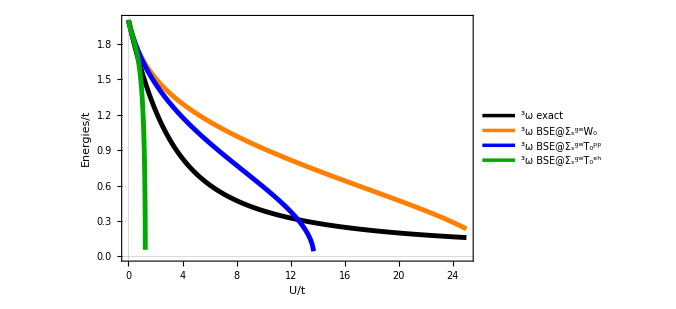

```mathematica
exctripletΣ=With[{t=1},ListPlot[
{Table[Flatten[{U,excas1[t,U,0.0]}],{U,0,25,0.1}],
Table[Flatten[{U,vtgwstat[t,U]}],{U,0,25,0.1}],
Table[Flatten[{U,vtstatΣgwTpptriplet[t,U]}],{U,0,25,0.1}],
Table[Flatten[{U,vtstatΣgwTphtriplet[t,U]}],{U,0,25,0.001}]},
Joined->True,PlotLegends->{"^3ω exact","^3ω BSE@Σ_s^gwW_0","^3ω BSE@Σ_s^gwT_0^pp","^3ω BSE@Σ_s^gwT_0^eh"},Frame->True,FrameLabel->{"U/t","Energies/t"},LabelStyle->Directive[FontFamily->"Arial",Black,FontSize->20],FrameStyle->Directive[Black,Thick],ImageSize->500,PlotTheme->"Scientific",PlotStyle->{{Black,Thickness[0.007]},{Orange,Thickness[0.007]},{Blue,Thickness[0.007]},{Darker[Green],Thickness[0.007]}}
]]//Quiet
```

```mathematica
Export["BSE_SigmaGW_Xi_triplet.pdf",exctripletΣ]
```

BSE_SigmaGW_Xi_triplet.pdf

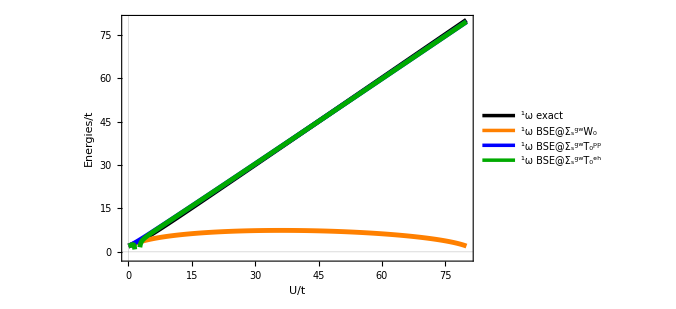

```mathematica
excsingletΣ=With[{t=1},ListPlot[
{Table[Flatten[{U,excas2[t,U,0.0]}],{U,0,80,0.1}],
Table[Flatten[{U,vsgwstat[t,U]}],{U,0,80,0.1}],
Table[Flatten[{U,vtstatΣgwTppsinglet[t,U]}],{U,0,80,0.1}],
Table[Flatten[{U,vtstatΣgwTphsinglet[t,U]}],{U,0,2.7,0.1}],
Table[Flatten[{U,-vtstatΣgwTphsinglet[t,U]}],{U,2.7,80,0.1}]},
Joined->True,PlotLegends->{"^1ω exact","^1ω BSE@Σ_s^gwW_0","^1ω BSE@Σ_s^gwT_0^pp","^1ω BSE@Σ_s^gwT_0^eh"},Frame->True,FrameLabel->{"U/t","Energies/t"},LabelStyle->Directive[FontFamily->"Arial",Black,FontSize->20],FrameStyle->Directive[Black,Thick],ImageSize->500,PlotTheme->"Scientific",PlotStyle->{{Black,Thickness[0.007]},{Orange,Thickness[0.007]},{Blue,Thickness[0.007]},{Darker[Green],Thickness[0.007]},{Darker[Green],Thickness[0.007]}}
]]//Quiet
```

```mathematica
Export["BSE_SigmaGW_Xi_singulet.pdf",excsingletΣ]
```

BSE_SigmaGW_Xi_singulet.pdf

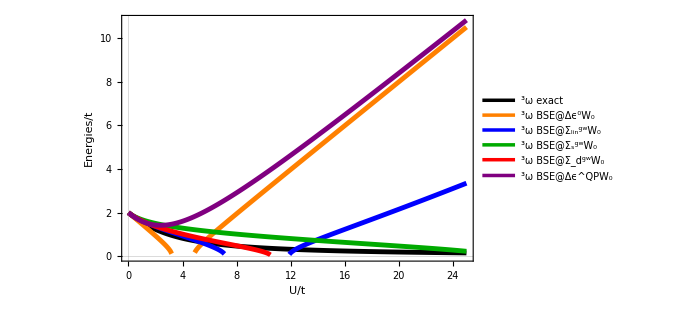

```mathematica
exctriplet=With[{t=1,Δv=0.000000},ListPlot[
{Table[Flatten[{U,excas1[t,U,Δv]}],{U,0,25,0.1}],
Table[Flatten[{U,vtgwgz[t,U]}],{U,0,25,0.1}],
Table[Flatten[{U,vtgwlin[t,U]}],{U,0,25,0.1}],
Table[Flatten[{U,vtgwstat[t,U]}],{U,0,25,0.1}],
Table[Flatten[{U,vtgwdyn[t,U]}],{U,0,25,0.1}],
Table[Flatten[{U,vtgwΔϵQP[t,U]}],{U,0,25,0.1}]},
Joined->True,PlotLegends->{"^3ω exact","^3ω BSE@Δϵ^0W_0","^3ω BSE@Σ_lin^gwW_0","^3ω BSE@Σ_s^gwW_0","^3ω BSE@Σ_d^gwW_0","^3ω BSE@Δϵ^QPW_0"},Frame->True,FrameLabel->{"U/t","Energies/t"},LabelStyle->Directive[FontFamily->"Arial",Black,FontSize->20],FrameStyle->Directive[Black,Thick],ImageSize->500,PlotTheme->"Scientific",PlotStyle->{{Black,Thickness[0.007]},{Orange,Thickness[0.007]},{Blue,Thickness[0.007]},{Darker[Green],Thickness[0.007]},{Red,Thickness[0.007]}, {Purple,Thickness[0.007]}}
]]//Quiet
```

```mathematica
Export["BSEGW_dim_sym_triplet.pdf",exctriplet]
```

BSEGW_dim_sym_triplet.pdf

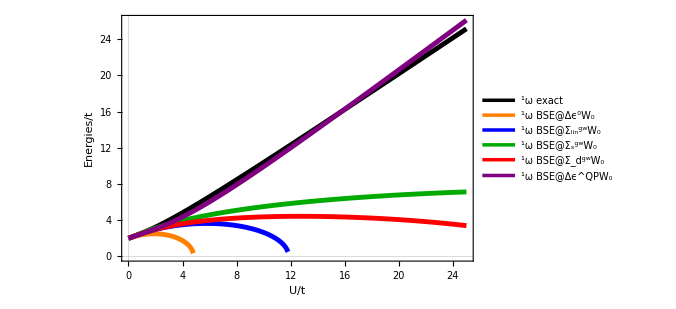

```mathematica
excsingulet=With[{t=1,Δv=0.000000},ListPlot[
{Table[Flatten[{U,excas2[t,U,Δv]}],{U,0,25,0.1}],
Table[Flatten[{U,vsgwgz[t,U]}],{U,0,25,0.1}],
Table[Flatten[{U,vsgwlin[t,U]}],{U,0,25,0.1}],
Table[Flatten[{U,vsgwstat[t,U]}],{U,0,25,0.1}],
Table[Flatten[{U,vsgwdyn[t,U]}],{U,0,25,0.1}],
Table[Flatten[{U,vsgwΔϵQP[t,U]}],{U,0,25,0.1}]},
Joined->True,PlotLegends->{"^1ω exact","^1ω BSE@Δϵ^0W_0","^1ω BSE@Σ_lin^gwW_0","^1ω BSE@Σ_s^gwW_0","^1ω BSE@Σ_d^gwW_0","^1ω BSE@Δϵ^QPW_0"},Frame->True,FrameLabel->{"U/t","Energies/t"},LabelStyle->Directive[FontFamily->"Arial",Black,FontSize->20],FrameStyle->Directive[Black,Thick],ImageSize->500,PlotTheme->"Scientific",PlotStyle->{{Black,Thickness[0.007]},{Orange,Thickness[0.007]},{Blue,Thickness[0.007]},{Darker[Green],Thickness[0.007]},{Red,Thickness[0.007]}, {Purple,Thickness[0.007]}}
]]//Quiet
```

```mathematica
Export["BSEGW_dim_sym_singulet.pdf",excsingulet]
```

BSEGW_dim_sym_singulet.pdf